MATH 8701 Homework 3

```mathematica
P[{x1_, x2_, x3_}]:= {x1/(1-x3),x2/(1-x3)};
Q[{x_,y_}]:= {2x/(x^2+y^2 + 1), 2y/(x^2+y^2 + 1), (x^2 + y^2-1)/(x^2+y^2 + 1)};
R[t_] = {{1, 0, 0},{0 , Cos[a*t],-Sin[a*t]},{0, Sin[a*t],Cos[a*t]}};
```

```mathematica
R[t].Q[{x,y}]
```

{(2 x)/(1+x^2+y^2),(2 y Cos[a t])/(1+x^2+y^2)-((-1+x^2+y^2) Sin[a t])/(1+x^2+y^2),((-1+x^2+y^2) Cos[a t])/(1+x^2+y^2)+(2 y Sin[a t])/(1+x^2+y^2)}

```mathematica
({{1, 0, 0}, {0, Cos[a t], -Sin[a t]}, {0, Sin[a t], Cos[a t]}}).({{(2 x)/(1+x^2+y^2)}, {(2 y)/(1+x^2+y^2)}, {(-1+x^2+y^2)/(1+x^2+y^2)}})
```

{(2 x)/(1+x^2+y^2),(2 y Cos[a t])/(1+x^2+y^2)-((-1+x^2+y^2) Sin[a t])/(1+x^2+y^2),((-1+x^2+y^2) Cos[a t])/(1+x^2+y^2)+(2 y Sin[a t])/(1+x^2+y^2)}

```mathematica
P@%
```

{(2 x)/((1+x^2+y^2) (1-((-1+x^2+y^2) Cos[a t])/(1+x^2+y^2)-(2 y Sin[a t])/(1+x^2+y^2))),((2 y Cos[a t])/(1+x^2+y^2)-((-1+x^2+y^2) Sin[a t])/(1+x^2+y^2))/(1-((-1+x^2+y^2) Cos[a t])/(1+x^2+y^2)-(2 y Sin[a t])/(1+x^2+y^2))}

```mathematica
D[%,t]/.t-> 0
```

{(4 a x y)/((1+x^2+y^2)^2 (1-(-1+x^2+y^2)/(1+x^2+y^2))^2),(4 a y^2)/((1+x^2+y^2)^2 (1-(-1+x^2+y^2)/(1+x^2+y^2))^2)-(a (-1+x^2+y^2))/((1+x^2+y^2) (1-(-1+x^2+y^2)/(1+x^2+y^2)))}

```mathematica
a=1;
F[x_,y_]=Simplify[{(4 a x y)/((1+x^2+y^2)^2 (1-(-1+x^2+y^2)/(1+x^2+y^2))^2),(4 a y^2)/((1+x^2+y^2)^2 (1-(-1+x^2+y^2)/(1+x^2+y^2))^2)-(a (-1+x^2+y^2))/((1+x^2+y^2) (1-(-1+x^2+y^2)/(1+x^2+y^2)))}]
```

{x y,1/2 (1-x^2+y^2)}

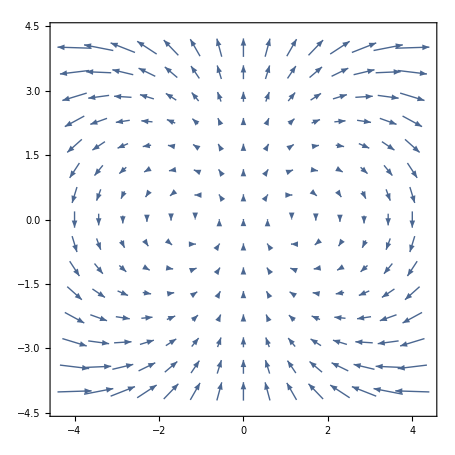

```mathematica
VectorPlot[F[x,y],{x,-4,4},{y,-4,4}]
```